```mathematica
Clear["Global`*"]
```

```mathematica
Needs["CUDALink`"]
```

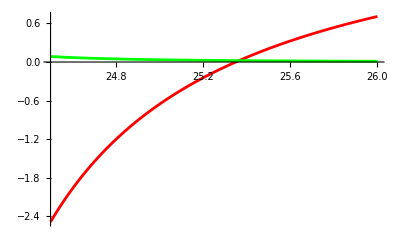

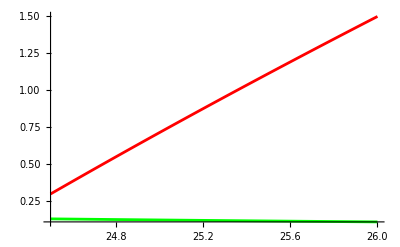

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(***************石墨烯****************)
Clear["Global`*"]
T=300;
KB=1.380649*10^-23;(*玻耳兹曼常数  kB=2.5852×e×10^-2*)
h=(6.626×10^-34)/(2 π);(*约化普朗克常数 *)
vF=10^6*10^9;(*费米速度 *)
e=1.6*10^-19;(*电子电荷 *)
μc=φ e;(*化学势 *)
φ=0.1460;
μ=κ×10^9×10^9;(*电子迁移率 *)
κ=3;
τ=(μc μ)/(e vF vF);(*弛豫时间 *)
σtotal=(I e^2 e φ)/(π h^2(ww+I/τ))+e^2/(4h)(HeavisideTheta[h ww-2 e φ]+(I Log[Abs[(h ww-2 e φ)/(h ww+2e φ)]])/π);(*总的电导率*)
dgra=0.35;(*石墨烯厚度*)
μ0=4π×10^-7×10^-9;(*真空磁导率*)
c=3×10^8×10^9;(*光速*)
ε0=1/(μ0 c^2);(*真空介电常数*)
ww=f*10^12*2Pi;(*频率*)
εlgra=1+(I σtotal)/(ww ε0 dgra);(*石墨烯面内介电常数*)
εtgra=3;(*石墨烯垂直介电常数*)
 
(***************氮化硼*****************)

εlhbn=εl((wlLo^2-w2^2-I taul w2)/(wlTo^2-w2^2-I taul w2));(*面内介电常数*)
εthbn=εt((wtLo^2-w2^2-I taut w2)/(wtTo^2-w2^2-I taut w2));(*面外介电常数*)
εl=5.1;(*高频介电常数*)
εt=2.5;(*声子阻尼*)
wlLo=1650*10^2;(*纵向光频率*)
wlTo=1394.5*10^2;(*横向光阻尼*)
wtLo=845*10^2;(*纵向光频率*)
wtTo=785*10^2;(*横向光阻尼*)
w2=f/(c2*10^-12);(*频率单位转化*)
c2=3*10^8;(*光速*)
taul=1.8*10^2;(*声子阻尼*)
taut=1*10^2;(*声子阻尼*)
dhbn=9;
Re[εlhbn];
Im[εlhbn];
Re[εthbn];
Im[εthbn];

(****************等效介质理论*********************)

εteff=(εtgra εthbn(dgra+dhbn))/(εthbn  dgra+εtgra  dhbn);(*垂直方向等效介电常数*)
εleff=(εlgra  dgra+εlhbn  dhbn)/(dgra+dhbn);(*水平方向等效介电常数*)
a=Re[εteff];
b=Im[εteff];
o=Re[εleff];
p=Im[εleff];
Plot[{Re[εteff],Im[εteff]},{f,24.5,26},PlotRange->All,PlotPoints->201,PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
Plot[{Re[εleff],Im[εleff]},{f,24.5,26},PlotRange->All,PlotPoints->201,PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
(***********菲尼尔反射系数*********)
rTM12=(Cos[θ]*εleff-Sqrt[(εleff-(εleff/εteff)*Sin[θ]*Sin[θ])])/(Cos[θ]*εleff+Sqrt[(εleff-(εleff/εteff)*Sin[θ]*Sin[θ])]);
rTE12=(Cos[θ]-Sqrt[(εleff-Sin[θ]*Sin[θ])])/(Cos[θ]+Sqrt[(εleff-Sin[θ]*Sin[θ])]);
tTM12=(2*εleff*Cos[θ])/(Cos[θ]*εleff+(εleff-(εleff/εteff)*Sin[θ]*Sin[θ])^1/2);
tTE12=(2*Cos[θ])/(Cos[θ]+(εleff-Sin[θ]*Sin[θ])^1/2);
(**)
rTM120=(Cos[θ]*o-Sqrt[(o-(o/a)*Sin[θ]*Sin[θ])])/(Cos[θ]*o+Sqrt[(o-(o/a)*Sin[θ]*Sin[θ])]);
rTE120=(Cos[θ]-Sqrt[(o-Sin[θ]*Sin[θ])])/(Cos[θ]+Sqrt[(o-Sin[θ]*Sin[θ])]);
tTM120=(2*o*Cos[θ])/(Cos[θ]*o+(o-(o/a)*Sin[θ]*Sin[θ])^1/2);
tTE120=(2*Cos[θ])/(Cos[θ]+(o-Sin[θ]*Sin[θ])^1/2);
θ=(α/180)*Pi;
RTM=(Abs[rTM12])^2;
RTE=(Abs[rTE12])^2;
TTM=1-RTM;
TTE=1-RTE;
(**)
RTM0=(Abs[rTM120])^2;
RTE0=(Abs[rTE120])^2;
TTM0=1-RTM0;
TTE0=1-RTE0;

DensityPlot[RTM0,{α,0,90},{f,24.5,26},PlotPoints->500,ColorFunction->"SunsetColors",PlotLegends->Automatic]
DensityPlot[RTE0,{α,0,90},{f,24.5,26},PlotPoints->500,ColorFunction->"SunsetColors",PlotLegends->Automatic]
DensityPlot[RTM0/RTE0,{α,0,90},{f,24.5,26},PlotPoints->500,ColorFunction->"SunsetColors",PlotLegends->Automatic]
DensityPlot[RTM/RTE,{α,0,90},{f,24.5,26},PlotPoints->500,ColorFunction->"SunsetColors",PlotLegends->Automatic]
```